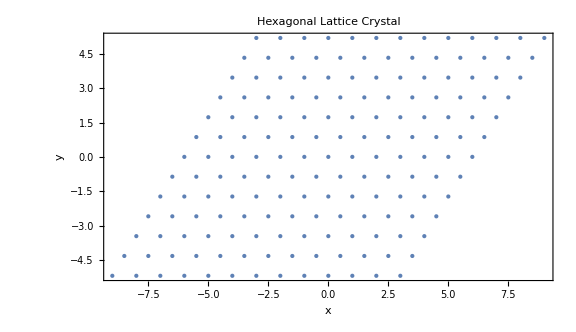

```mathematica
(* Hexagonal lattice skyrmion *)
a1={1,0}; (*Define the first lattice vector*)
a2={1/2,Sqrt[3]/2}; (*Define the second lattice vector*)
m = 1;
γ =0;
n=6; (*Number of lattice points in each direction - USE EVEN NO. ONLY*)
t=1;
ras =0;
HxX=Flatten[Table[a1*i+a2*j,{i,-n,n},{j,-n,n}],1];
plot1 = ListPlot[HxX,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Hexagonal Lattice Crystal", ImageSize->Large]
```

```mathematica
basis = {{0,1}, {Sqrt[3]/2,-1/2}, { -Sqrt[3]/2,-1/2}};
q =  Pi/(3 * Sqrt[3]){{2 Sqrt[3], 0},{-Sqrt[3], -3},{-Sqrt[3], 3}};
phase={ Pi,Pi,Pi};
mxy [x_, y_] := Total[Table[(Sin[q[[i]].{x,y}+phase[[i]] ]) basis[[i]],{i,1,3}]];
mz[x_, y_] := Total[Table[(Cos[q[[i]].{x,y} +phase[[i]]]),{i,1,3}]];
spins[x_, y_] := {N[mxy[x, y].{1,0}],N[ mxy[x, y].{0,1}], N[mz[x,y]]};
mxy[x, y]
mz[x,y]
```

{-1/2 √3 Sin[(π x)/3-(π y)/(√3)]+1/2 √3 Sin[(π x)/3+(π y)/(√3)],-Sin[(2 π x)/3]-1/2 Sin[(π x)/3-(π y)/(√3)]-1/2 Sin[(π x)/3+(π y)/(√3)]}

-Cos[(2 π x)/3]-Cos[(π x)/3-(π y)/(√3)]-Cos[(π x)/3+(π y)/(√3)]

```mathematica
OPvector = Table[{HxX[[i]][[1]],HxX[[i]][[2]],0},{i,1,Length[HxX]}];
sfield =Chop[N[Table[spins[HxX[[i]][[1]], HxX[[i]][[2]]],{i, 1, Length[HxX]}]]];
spinfield = Table[sfield[[i]]/Norm[sfield[[i]]],{i,1,Length[sfield]}];
cylinders = Table[
{{ColorData["Rainbow"][Rescale[spinfield[[i]][[3]],{-1,1}]],Cylinder[{OPvector[[i]]-spinfield[[i]]/2,OPvector[[i]]},1/10]}},{i,1,Length[HxX] }
];
cones= Table[
{{ColorData["Rainbow"][Rescale[spinfield[[i]][[3]],{-1,1}]],
Cone[{OPvector[[i]],OPvector[[i]]+spinfield[[i]]/2},1/5]}},
{i,1,Length[HxX] }
];
jjjjj=Graphics3D[{cylinders,cones},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Full, Lighting->{{"Ambient",White}} ]
```

-Graphics3D-

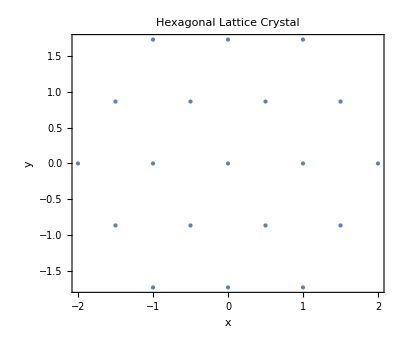

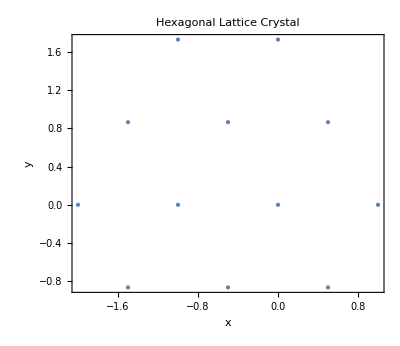

{{-2,0},{-3/2,(√3)/2},{-1,√3},{-3/2,-(√3)/2},{-1,0},{-1/2,(√3)/2},{0,√3},{-1/2,-(√3)/2},{0,0},{1/2,(√3)/2},{1/2,-(√3)/2},{1,0}}

-Graphics-

```mathematica
SkX = Table[If[Norm[HxX[[i]]]<=2, HxX[[i]]],{i, 1 , Length[HxX],1}];
SkX//MatrixForm;
SkUnitOP = DeleteCases[SkX,Null];
SkUnitOP // MatrixForm;
ListPlot[SkUnitOP,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Hexagonal Lattice Crystal"]

For[i = 0,i<= 2,i++,
v = i *a1 + (2-i)*a2;
SkUnitOP = DeleteCases[SkUnitOP,v];
SkUnitOP = DeleteCases[SkUnitOP,{v[[1]], - v[[2]]}];
SkUnitOP = DeleteCases[SkUnitOP,{-i, - Sqrt[3]}];
] 
ListPlot[SkUnitOP,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Hexagonal Lattice Crystal"]


listac= Table[SkUnitOP[[i]]+{0,0},{i,1,Length[SkUnitOP]}]
ListPlot[listac,AspectRatio->Automatic,PlotStyle->PointSize[Large],Frame->True,FrameLabel->{"x","y"},PlotLabel->"Hexagonal Lattice Crystal"]


OPvector1 = Table[{listac[[i]][[1]],listac[[i]][[2]],0},{i,1,Length[listac]}];
sfield1 =Chop[N[Table[spins[listac[[i]][[1]], listac[[i]][[2]]],{i, 1, Length[listac]}]]];
spinfield1 = Table[sfield1[[i]]/Norm[sfield1[[i]]],{i,1,Length[sfield1]}];
cylinders1 = Table[
{{ColorData["Rainbow"][Rescale[spinfield1[[i]][[3]],{0,1}]],Cylinder[{OPvector1[[i]]-spinfield1[[i]]/2,OPvector1[[i]]},1/10]}},{i,1,Length[listac] }
];
cones1= Table[
{{ColorData["Rainbow"][Rescale[spinfield1[[i]][[3]],{0,1}]],
Cone[{OPvector1[[i]],OPvector1[[i]]+spinfield1[[i]]/2},1/5]}},
{i,1,Length[listac] }
];
jjjj=Graphics3D[{cylinders1,cones1},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"},PlotRange->All,  ImageSize->Full, Lighting->{{"Ambient",White}} ];
```

```mathematica
spinfield1;
polarterms=CoordinateTransform["Cartesian"->"Spherical",spinfield1]/.Indeterminate->0;
polarterms//MatrixForm
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

General::stop: Further output of ArcTan::indet will be suppressed during this calculation.

(1. | 0. | 0
1. | 0. | 0
1. | 0. | 0
1. | 0. | 0
1. | 1.85183 | 1.5708
1. | 1.85183 | 0.523599
1. | 0. | 0
1. | 1.85183 | 2.61799
1. | 3.14159 | 0
1. | 1.85183 | -0.523599
1. | 1.85183 | -2.61799
1. | 1.85183 | -1.5708)

```mathematica
θ = Table[polarterms[[i]][[2]],{i,1,Length[polarterms]}];
ϕ =Table[polarterms[[i]][[3]],{i,1,Length[polarterms]}];
NN1 = {5,6,7,8,9,10,1,11,12,4,2,3};
NN2 = {7,11,12,10,1,2,3,4,5,6,8,9};
NN3 = {2,3,8,5,6,7,11,9,10,1,12,4};
NN4 = {4,5,6,3,8,9,10,7,11,12,1,2};
NN5 = {11,12,4,1,2,3,8,5,6,7,9,10};
NN6 = {10,1,2,12,4,5,6,3,8,9,7,11};
```

```mathematica
KetArray = Table[{Cos[1/2 θ⟦i⟧], Sin[1/2 θ⟦i⟧] ⅇ^(ⅈ ϕ⟦i⟧)},{i,1,Length[polarterms]}]//Chop;
KetArray// MatrixForm;
(* The conjugate vector of the spin texture |χ⟩, ⟨χ|:=|χ⟩† *)
BraArray = Table[Conjugate[KetArray[[i]]],{i,1,Length[KetArray]}];
```

```mathematica
K[kx_, ky_] := {kx, ky}
(* Hamiltonian matrix *)
Hij[kx_, ky_, ras_] := Module[{hopingProduct},
hopingProduct = ConstantArray[0,{Length[polarterms],Length[polarterms]}];
For[i = 1, i<= Length[polarterms], i++,
hopingProduct[[i]][[NN1[[i]]]] =  t BraArray[[i]].KetArray[[NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].{1,0})   +   ras*I* BraArray[[i]].(-PauliMatrix[2]).KetArray[[NN1[[i]]]] ⅇ^(ⅈ K[kx,ky].{1,0});

hopingProduct[[i]][[NN2[[i]]]] =  t BraArray[[i]].KetArray[[NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1,0}) +   ras*I* BraArray[[i]].(PauliMatrix[2]).KetArray[[NN2[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1,0});

hopingProduct[[i]][[NN3[[i]]]] =t BraArray[[i]].KetArray[[NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].{1/2,(√3)/2}) + ras*I* BraArray[[i]].((√3)/2 PauliMatrix[1] - 1/2 PauliMatrix[2] ).KetArray[[NN3[[i]]]] ⅇ^(ⅈ K[kx,ky].{1/2,(√3)/2}) ; 
hopingProduct[[i]][[NN4[[i]]]] =  t BraArray[[i]].KetArray[[NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].{1/2,(-√3)/2})   +ras*I* BraArray[[i]].((-√3)/2 PauliMatrix[1] - 1/2 PauliMatrix[2] ).KetArray[[NN4[[i]]]] ⅇ^(ⅈ K[kx,ky].{1/2,(-√3)/2});
hopingProduct[[i]][[NN5[[i]]]] =  t BraArray[[i]].KetArray[[NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1/2,(√3)/2})   + ras*I* BraArray[[i]].((√3)/2 PauliMatrix[1] + 1/2 PauliMatrix[2] ).KetArray[[NN5[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1/2,(√3)/2});
hopingProduct[[i]][[NN6[[i]]]] =  t BraArray[[i]].KetArray[[NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1/2,(-√3)/2})   +   ras*I* BraArray[[i]].((-√3)/2 PauliMatrix[1] + 1/2 PauliMatrix[2] ).KetArray[[NN6[[i]]]] ⅇ^(ⅈ K[kx,ky].{-1/2,(-√3)/2});
hopingProduct[[i]][[i]] = 0;];
hopingProduct
]
```

```mathematica
(* Eigenvalue function *)
Ev[kx_,ky_, ras_] := Sort[Eigenvalues[Hij[kx, ky, ras]] ]
(* Collection of Eigen values along the irreducible path in the reciprocal space *)
d=25; (* step count *)
tabGK[n_, ras_]:=Table[Ev[k,k/(√3),ras][[n]],{k,0, Pi/(3),Pi/(3 * d)}];
tabKM[n_, ras_]:=Table[Ev[π/3,ky,ras][[n]],{ky,Pi/(3 √3),0,-Pi/(3 √3*d)}];
tabMG[n_, ras_]:=Table[Ev[kx,0,ras][[n]],{kx,Pi/(3),0,-Pi/(3*0.87*d)}];

l1=Length[tabGK[1, ras]];
l2=l1+Length[tabKM[1,ras]];
l3=l2+Length[tabMG[1,ras]];
customTicksX={{0,Style["Γ",Bold]},{l1,Style["K",Bold]},{l2,Style["M",Bold]},{l3,Style["Γ",Bold]}};

vl1=Graphics[{Line[{{l1,-20},{l1,20}}]},AspectRatio->1];
vl2=Graphics[{Line[{{l2,-20},{l2,20}}]},AspectRatio->1];
```

```mathematica
band1=Join[tabGK[1, ras],tabKM[1, ras],tabMG[1, ras]];
band2=Join[tabGK[2, ras],tabKM[2, ras],tabMG[2, ras]];
band3=Join[tabGK[3, ras],tabKM[3, ras],tabMG[3, ras]];
band4=Join[tabGK[4, ras],tabKM[4, ras],tabMG[4, ras]];
band5=Join[tabGK[5, ras],tabKM[5, ras],tabMG[5, ras]];
band6=Join[tabGK[6, ras],tabKM[6, ras],tabMG[6, ras]];
band7=Join[tabGK[7, ras],tabKM[7, ras],tabMG[7, ras]];
band8=Join[tabGK[8, ras],tabKM[8, ras],tabMG[8, ras]];
band9=Join[tabGK[9, ras],tabKM[9, ras],tabMG[9, ras]];
band10=Join[tabGK[10, ras],tabKM[10, ras],tabMG[10, ras]];
band11=Join[tabGK[11, ras],tabKM[11, ras],tabMG[11, ras]];
band12=Join[tabGK[12, ras],tabKM[12, ras],tabMG[12, ras]];
```

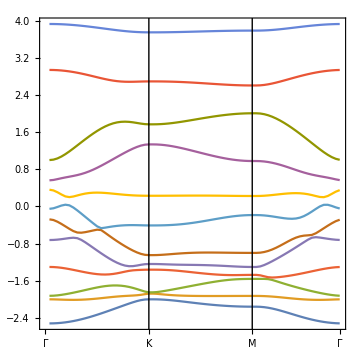

```mathematica
plot=ListLinePlot[{band1,band2,band3,band4,band5,band6,band7,band8,band9,band10,band11,band12},ImageSize->Medium,AspectRatio->1,PlotRange->All,FrameTicks->{{Automatic,None},{customTicksX,None}},Axes->False,Frame->True,FrameTicksStyle->Directive[Bold,Black]];

Show[plot,vl1,vl2]
```

```mathematica
join[i_, ras_]:= Join[tabGK[i, ras],tabKM[i, ras],tabMG[i, ras]]
bands[ras_] := Table[join[i,ras],{i,1,Length[listac]}];
plotting[ras_]:=Show[ListLinePlot[bands[ras],ImageSize->Medium,AspectRatio->1,FrameTicks->{{Automatic,None},{customTicksX,None}},Axes->False,Frame->True,PlotLabel->"12 Site Skyrmion Model in Triangular Lattice",PlotRange->{{1,l3},{-3,4.8}}, FrameTicksStyle->Directive[Bold,Black]], vl1, vl2];
```

```mathematica
(*Animation code*)
animation = Animate[Column[{plotting[rashba],Text["Rashba coupling: "<>ToString[rashba]]}],{{rashba,0,"Rashba strength"},0.26,1,0.02},AnimationRunning->False]
```